## Lesson 25: impulse functions

## Overview

In many applications, you may want to describe a function that acts over a very short interval of time.

In this lesson you will construct a special function known as the DiracDelta function and then solve differential equations that have a DiracDelta nonhomogeneous term:

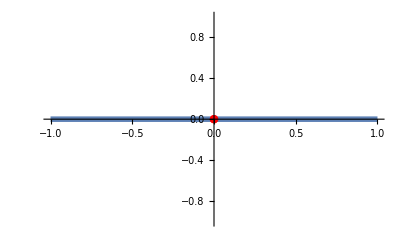

```mathematica
Plot[DiracDelta[t],{t,-1,1},]
```

## Construct DiracDelta

Consider the function:

g(t,s)=Piecewise[{{1/(2 s), -s < t < s}, {0, Otherwise}}]

You can define this using Piecewise:

```mathematica
g[t_,s_]:=Piecewise[{{1/(2 s),-s<t<s},{0,t>=s},{0,t<=-s}}]
```

It is important to observe this function for different values of s:

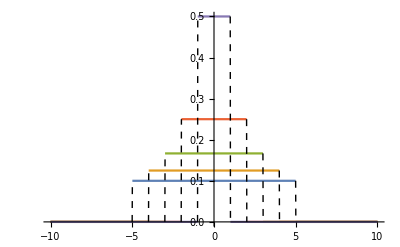

```mathematica
Plot[{g[t,5],g[t,4],g[t,3],g[t,2],g[t,1]},{t,-10,10},]
```

## Construct DiracDelta

The length of the area is always 2s and the height is always defined to be 1/(2s). So you would expect the area highlighted to always remain constant at 1:

```mathematica
Manipulate[Plot[g[t,s],{t,-5,5},],{s,0.2,4}]
```

## Construct DiracDelta

Integrate the function to confirm the hypothesis that the integral is always 1:

```mathematica
Integrate[g[t,s],{t,-∞,∞}]
```

Piecewise[{{1, s>0}, {0, True}}]

Then, by taking the Limit as s→0, you can construct the DiracDelta function δ(t):

δ(t)=lim_(s→0) g(t,s)

```mathematica
Limit[g[t,s],{s->0}]
```

ConditionalExpression[0, t≠0]

## Construct Dirac Delta

The important properties of the DiracDelta function are that:

δ(t)=Piecewise[{{Indeterminate, t=0}, {0, Otherwise}}]

and the fact that:

∫_(-∞)^∞ δ(t)ⅆt=1

Because

L{δ(t)}=L{lim_(s→ 0) g(t,s)}=lim_(s→ 0) L{g(t,s)},

you can also prove the following surprising result:

```mathematica
LaplaceTransform[DiracDelta[t],t,s]
```

1

With this, you can solve differential equations with impulse functions.

## Example 1

Find the solution of the differential equation:

y''(t)+y(t)=δ(t-1)

y(0)=0

y'(0)=0

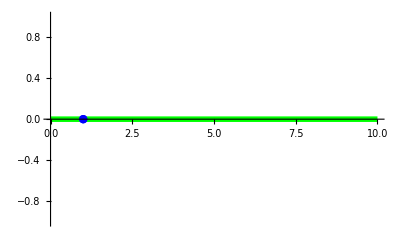

```mathematica
Plot[DiracDelta[t-1],{t,0,10},]
```

Define the differential equation:

```mathematica
eqn=y''[t]+y[t]==DiracDelta[t-1];
```

## Example 1

Apply LaplaceTransform to the equation:

```mathematica
lt=LaplaceTransform[eqn,t,s]
```

LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0]==ⅇ^-s

Replace y(0) and y'(0) with their respective values:

```mathematica
lt2=lt/.{y[0]->0,y'[0]->0}
```

LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]==ⅇ^-s

Solve for L{y(t)}:

```mathematica
Solve[lt2,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→ⅇ^-s/(1+s^2)}}

Apply the function InverseLaplaceTransform to recover the solution to the differential equation:

```mathematica
sln=InverseLaplaceTransform[ⅇ^-s/(1+s^2),s,t]
```

-HeavisideTheta[-1+t] Sin[1-t]

## Example 1

You can visually see how the forcing term initially affects the solution and later has no effect:

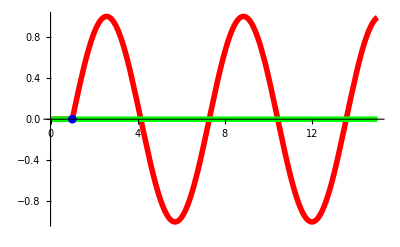

```mathematica
Show[Plot[sln,{t,0,15},],Plot[DiracDelta[t-1],{t,0,15},]]
```

You can use DSolveValue to verify this result:

```mathematica
sln2=DSolveValue[{eqn,y[0]==0,y'[0]==0},y[t],t];
```

Plot the result from DSolveValue:

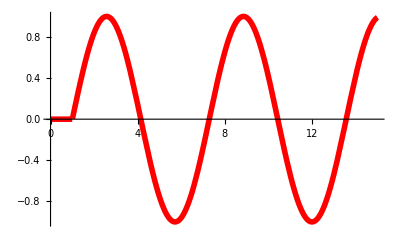

```mathematica
Plot[sln2,{t,0,15},]
```

## Example 2

Find the solution of the differential equation:

2 y''(t)+y'(t)+2 y(t)=-δ(t-2 π)+δ(t-3 π)

y(0)=0

y'(0)=0

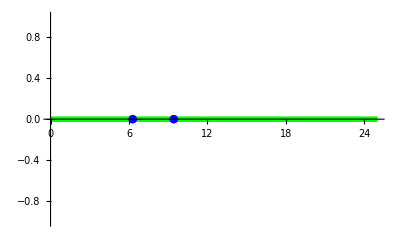

```mathematica
Plot[-DiracDelta[t-2Pi]+DiracDelta[t-3Pi],{t,0,25},]
```

Define the differential equation:

```mathematica
eqn=2y''[t]+y'[t]+2y[t]==-DiracDelta[t-2Pi]+DiracDelta[t-3Pi];
```

## Example 2

Apply LaplaceTransform to the equation:

```mathematica
lt=LaplaceTransform[eqn,t,s]
```

2 LaplaceTransform[y[t],t,s]+s LaplaceTransform[y[t],t,s]-y[0]+2 (s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0])==ⅇ^(-3 π s)-ⅇ^(-2 π s)

Replace y(0) and y'(0) with their respective values:

```mathematica
lt2=lt/.{y[0]->0,y'[0]->0}
```

2 LaplaceTransform[y[t],t,s]+s LaplaceTransform[y[t],t,s]+2 s^2 LaplaceTransform[y[t],t,s]==ⅇ^(-3 π s)-ⅇ^(-2 π s)

Solve for L{y(t)}:

```mathematica
Solve[lt2,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→-(ⅇ^(-3 π s) (-1+ⅇ^(π s)))/(2+s+2 s^2)}}

Apply the function InverseLaplaceTransform to recover the solution to the differential equation:

```mathematica
sln=InverseLaplaceTransform[-(ⅇ^(-3 π s) (-1+ⅇ^(π s)))/(2+s+2 s^2),s,t]
```

(2 ⅇ^(1/4 (3 π-t)) HeavisideTheta[-3 π+t] Sin[1/4 √15 (-3 π+t)])/(√15)-(2 ⅇ^(1/4 (2 π-t)) HeavisideTheta[-2 π+t] Sin[1/4 √15 (-2 π+t)])/(√15)

## Example 2

You can observe the positive and negative effects the forcing function has on the solution:

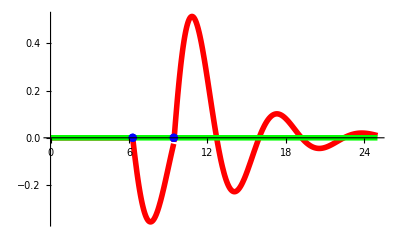

```mathematica
Show[Plot[sln,{t,0,25},],Plot[-DiracDelta[t-2Pi]+DiracDelta[t-3Pi],{t,0,25},]]
```

Use DSolveValue to verify this result:

```mathematica
sln2=DSolveValue[{eqn,y[0]==0,y'[0]==0},y[t],t];
```

Plot the result from DSolveValue:

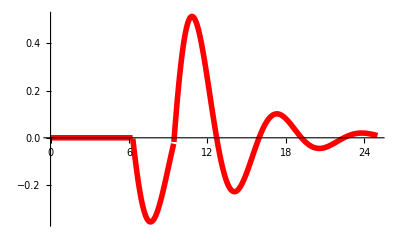

```mathematica
Plot[sln2,{t,0,25},]
```

## Example 2

A comparison to the homogeneous equation reveals the impact the forcing term has on the solution:

```mathematica
Plot[sln2,{t,0,25},]
```

-Graphics-

Define the homogeneous equation:

```mathematica
eqn2=2y''[t]+y'[t]+2y[t]==0;
```

Solve the homogeneous equation with DSolveValue:

```mathematica
sln3=DSolveValue[{eqn2,y[0]==1,y'[0]==0},y[t],t];
```

Plot the solution to the homogeneous equation:

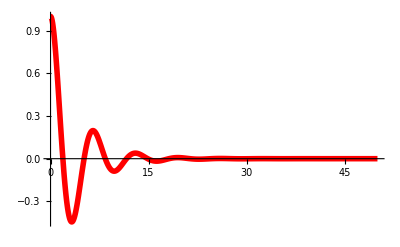

```mathematica
Plot[sln3,{t,0,50},]
```

## Summary

In this lesson, you constructed a new function called the DiracDelta function.

You examined how this forcing function influenced solutions to differential equations:

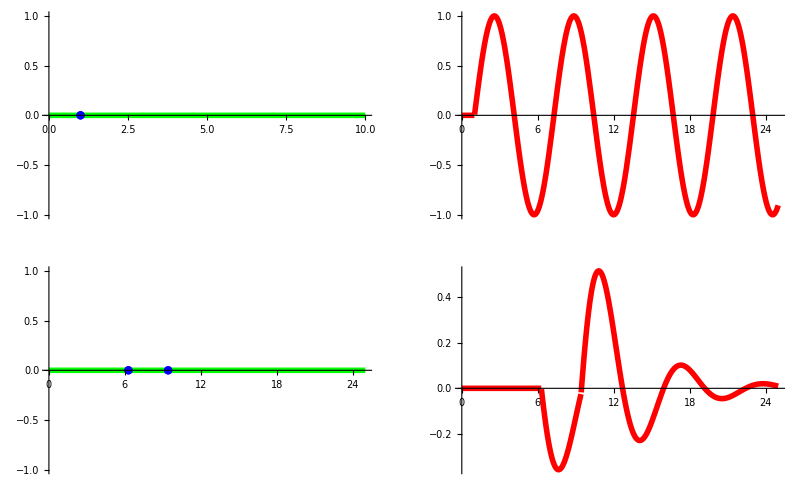

```mathematica
GraphicsGrid[{{
Plot[DiracDelta[t-1],{t,0,10},],Plot[Evaluate@DSolveValue[{y''[t]+y[t]==DiracDelta[t-1],y[0]==0,y'[0]==0},y[t],t],{t,0,25},]},{Plot[-DiracDelta[t-2Pi]+DiracDelta[t-3Pi],{t,0,25},],Plot[Evaluate@DSolveValue[{2y''[t]+y'[t]+2y[t]==-DiracDelta[t-2Pi]+DiracDelta[t-3Pi],y[0]==0,y'[0]==0},y[t],t],{t,0,25},]}}]
```